# Data Dependence

## Definitions

Let S_1 and S_2 be two statements, we define:

IN(S_1) — The set of variables used in S_1

OUT(S_1) — The set of variables written in S_1

Flow Dependence (S_1 δ^f S_2) — variable written and then used (RAW) … OUT(S_1)∩IN(S_2)≠ ∅

Anti-Dependence (S_1 δ^a S_2) — variable used and then written (WAR) … IN(S_1)∩OUT(S_2)≠ ∅

Output Dependence (S_1 δ^o S_2) — variable written and then written (WAW) … OUT(S_1)∩OUT(S_2)≠ ∅

Input Dependence (S_1 δ^I S_2) — variable used and then used (RAR) … IN(S_1)∩IN(S_2)≠ ∅

Dependence (S_1 δ^*S_2) — S_1 δ^f S_2∨S_1 δ^a S_2∨S_1 δ^o S_2

Consider the program:

1. A = 0
2. B = A
3. A = B + 1
4. C = A
5. S = &G
6. T = &G
7. *S = 3
8. *B = 4
9. Q = *A

Address Based dependence:

Value Based dependence: (subset of address based dependence)

Index Variable Interation Vector (i^iv=(I_1
I_2
⋮
I_n)) —

## Data Dependence

```mathematica
OUT[stmt_]:=Cases[{stmt},Inactive[Set][var_,___]->var];
IN[stmt_]:=Module[{r},
r=Cases[{stmt},Inactive[Set][_,rest___]->rest];
r=r/.{Inactive[_][rest___]->{rest}};
r=Flatten[r];
Select[r,Head[#]===Symbol&]
]
```

```mathematica
FlowDependence[s1_,s2_]:=Intersection[OUT[s1],IN[s2]]
AntiDependence[s1_,s2_]:=Intersection[IN[s1],OUT[s2]]
OutputDependence[s1_,s2_]:=Intersection[OUT[s1],OUT[s2]]
```

```mathematica
ClearAll[s1,s2,s3,s4,x,a,b,c,d]
s1=Inactivate[x=a+b];
s2=Inactivate[y=x+c];
s3=Inactivate[x=c+d];
s4=Inactivate[x=x+d];
Through[{IN,OUT}[s1]]
Through[{IN,OUT}[s2]]
```

{{a,b},{x}}

{{x,c},{y}}

```mathematica
Through[{FlowDependence,AntiDependence,OutputDependence}[s1,s2]]
```

{{x},{},{}}

```mathematica
Through[{FlowDependence,AntiDependence,OutputDependence}[s2,s1]]
```

{{},{x},{}}

```mathematica
Through[{FlowDependence,AntiDependence,OutputDependence}[s1,s3]]
```

{{},{},{x}}

```mathematica
gFlowDependence[pts_,e_]:={Arrowheads[{{.1,0.9}}],Arrow[pts]}
gAntiDependence[pts_,e_]:={Arrowheads[{{0.02,0.5,Graphics[{Thick,Line[{{0,1},{0,-1}}]}]},{.1,0.9}}],Arrow[pts]}
gOutputDependence[pts_,e_]:={Arrowheads[{{0.02,0.5,Graphics[{Thick,Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]}]},{.1,0.9}}],Arrow[pts]}
gInputDependence[pts_,e_]:={Arrowheads[{{0.02,0.5,Graphics[{Thick,Circle[]}]},{.1,0.9}}],Arrow[pts]}
panelLabel[lbl_]:=Panel[lbl,FrameMargins->0,Background->Directive[Yellow,Opacity[0.1]]]
```

```mathematica
DependenceGraph[stmts_]:=
Module[{subs=Subsets[stmts,{2}],s1,s2,v1,v2,edges,type,isFlowDependence,isAntiDependence,isOutputDependence,edge,sub},
edges={};
isFlowDependence[s1_,s2_]:=FlowDependence[s1,s2]=!={};
isAntiDependence[s1_,s2_]:=AntiDependence[s1,s2]=!={};
isOutputDependence[s1_,s2_]:=OutputDependence[s1,s2]=!={};
Do[
{s1,s2}=sub;
v1=First[Flatten[Position[stmts,s1]]];
v2=First[Flatten[Position[stmts,s2]]];
edge=Which[
isAntiDependence[s1,s2],
Property[v1->v2,EdgeShapeFunction->gAntiDependence],
isFlowDependence[s1,s2],
Property[v1->v2,EdgeShapeFunction->gFlowDependence],
isOutputDependence[s1,s2],
Property[v1->v2,EdgeShapeFunction->gOutputDependence],
True,
Property[v1->v2,EdgeShapeFunction->gInputDependence]
];
AppendTo[edges,edge],
{sub,subs}
];
Graph[edges,
VertexLabels->Table[i->Placed[stmts[[i]],Center,panelLabel],{i,Length[stmts]}],ImagePadding->50,BaselinePosition->Axis]
]
```

```mathematica
DependenceGraph[{s1,s2}]
```

-Graphics-

```mathematica
DependenceGraph[{s2,s1}]
```

-Graphics-

```mathematica
DependenceGraph[{s1,s3}]
```

-Graphics-

```mathematica
DependenceGraph[{s1,s2,s3,s4}]
```

-Graphics-

```mathematica
ClearAll[s1,s2,s3,s4,x,a,b,c,d]
s1=Inactivate[a=0];
s2=Inactivate[b=a];
s3=Inactivate[a=b+1];
s4=Inactivate[c=a];
```

```mathematica
DependenceGraph[{s1,s2,s3,s4}]
```

-Graphics-

## Finding Data Dependence

It is easy to see whether you choose ZIV, SIV, … but still not sure when to use the complicated tests. Based on program analysis [Goff, Kennedy, Tseng - PLDI ’91], we find that 53% of statements use ZIV, 46% SIV, and 3% MIV.

### GCD Test

The GCD test is a simple check to see if a dependence is possible. It can give false positives, but would never give a false negative. It does not find the distance vector and is only useful for existance check. Useful for testing non-linear subscripts.

If you acesses are a_1 i_1+a_2 i_2+…+a_n i_n+k and b_1 i_1+b_2 i_2+...+b_n i_n+m then a dependence exists only if a_1 i_1+a_2 i_2+…+a_n i_n+k = b_1 j_1+b_2 j_2+...+b_p j_p+m where i_1,i_2,…,i_n and j_1,…,j_p are iteration variables. Rewriting the formula we get a_1 i_1+…+a_n i_n-b_1 j_1-…-b_p j_p=m-k. This is a linear Diophantine equation, where an integer solution for x and y exist iff GCD(a_1,…, a_n,-b_1,…,-b_p) divides m-k. So if the check does not pass, then there is no possible dependence.

Consider the statment X[2*ii+3] = X[2*ii] + 50. To find if there is a loop carried dependence, we need to solve the equation x*ii1+k=y*ii2+m (where ii1 and ii2 are the iteration variables), or x*ii1 - y*ii2 = m - k. Since GCD(2,2)=2 does not divide -3 then no dependence is possible.

Suppose you have the following flow dependence:

1. for (int ii = 0; ii < n; ii++) {
2. 	a[4*ii + 2] = ...;
3. 	... = a[2*ii + 4];
4. }

Now, since GCD(4,2)=2 does divides 4-2=2 then a dependence is possible.

### ZIV Test (zero induction variables)

Pair of the subscripts of the form c_1 and c_2 where c_1 and c_2 are constants. If c_1≠c_2 then a dependence does not exist.

### Strong SIV Test (single induction variable, with identical strides)

See Practical Dependence Testing and https://sites.google.com/site/parallelizationforllvm/dependence-test

Have a pair of subscripts of the form c_1+a_1 ii and c_2+a_2 ii with a_1=a_2. We can prove independence using the GCD test (does a divide c_1-c_2), otherwise we compute the distance by solving c_1+a_1 ii_1=c_2+a_2 ii_2. We get the dependence distance d = ii_2-ii=(c_1-c_2)/a. A dependence exists iff d is an integer and Abs[d] < U-L where U, L are the loop’s upper and lower bounds. If a dependence exists, then the direction dir=Piecewise[{{<, d>0}, {=, d==0}, {>, d<0}}].

```mathematica
StrongSIV[U_,Inactive[Plus][c1_,Inactive[Times][a_,ii_]],Inactive[Plus][c2_,Inactive[Times][a_,ii2_]]]:=
Module[{d=(c1-c2)/a,r},
r=If[IntegerQ[d]&&Abs[d]<U,
"<",
"Unknown"
];
{d,r}
]
```

Example:

1. for (int ii = 0; ii < 8; ii++) {
2. 	a[ii + 1] = ...;
3. 	... = a[ii + 1];
4. }

```mathematica
StrongSIV[8,Inactivate[1+1*ii],Inactivate[1+1*ii]]
```

{0,<}

Example:

1. for (int ii = 0; ii < 8; ii++) {
2. 	a[ii + 1] = ...;
3. 	... = a[ii + 0];
4. }

```mathematica
StrongSIV[8,Inactivate[1+1*ii],Inactivate[0+1*ii]]
```

{1,<}

Example: (fails because d is not an integer)

1. for (int ii = 0; ii < 8; ii++) {
2. 	a[2*ii + 1] = ...;
3. 	... = a[2*ii + 0];
4. }

```mathematica
StrongSIV[8,Inactivate[1+2*ii],Inactivate[0+2*ii]]
```

{1/2,Unknown}

Example: (fails because it is outside the loop bounds)

1. for (int ii = 0; ii < 8; ii++) {
2. 	a[2*ii + 16] = ...;
3. 	... = a[2*ii + 0];
4. }

```mathematica
StrongSIV[8,Inactivate[16+2*ii],Inactivate[0+2*ii]]
```

{8,Unknown}

### Weak-zero SIV (single induction variable, with one stride equal to 0)

Have a pair of subscripts of the form c_1+a ii and c_2. Solving c_1+a ii=c_2. We get the dependence distance d =(c_1-c_2)/a. A dependence exists iff d is an integer  and Abs[d] < U-L where U, L are the loop’s upper and lower bounds. If a dependence exists, then the direction dir=Piecewise[{{<, d>0}, {=, d==0}, {>, d<0}}].

```mathematica
WeakZeroSIV[U_,Inactive[Plus][c1_,Inactive[Times][a_,ii_]],c2_]:=
Module[{d=(c1-c2)/a,r},
r=If[IntegerQ[d]&&Abs[d]<U,
"<",
"Unknown"
];
{d,r}
]
```

Example:

1. for (int ii = 0; ii < 8; ii++) {
2. 	a[ii + 1] = ...;
3. 	... = a[1];
4. }

```mathematica
WeakZeroSIV[8,Inactivate[1+1*ii],1]
```

{0,<}

Example:

1. for (int ii = 0; ii < 8; ii++) {
2. 	a[ii + 1] = ...;
3. 	... = a[0];
4. }

```mathematica
WeakZeroSIV[8,Inactivate[1+1*ii],0]
```

{1,<}

Example: (fails because d is not an integer)

1. for (int ii = 0; ii < 8; ii++) {
2. 	a[2*ii + 1] = ...;
3. 	... = a[0];
4. }

```mathematica
WeakZeroSIV[8,Inactivate[1+2*ii],0]
```

{1/2,Unknown}

Example: (fails because it is outside the loop bounds)

1. for (int ii = 0; ii < 8; ii++) {
2. 	a[ii] = ...;
3. 	... = a[8];
4. }

```mathematica
WeakZeroSIV[8,Inactivate[0+1*ii],8]
```

{-8,Unknown}

### Weak-crossing SIV (single induction variable, with one stride the negative of the other)

See Practical Dependence Testing and https://sites.google.com/site/parallelizationforllvm/dependence-test

Have a pair of subscripts of the form c_1+a ii and c_2. Solving c_1-a ii=c_2. We get the dependence distance d =(c_1-c_2)/(2a). A dependence exists iff d is an integer  and Abs[d] < U-L where U, L are the loop’s upper and lower bounds. If a dependence exists, then the direction dir=Piecewise[{{<, d>0}, {=, d==0}, {>, d<0}}].

```mathematica
WeakCrossingSIV[U_,Inactive[Plus][c1_,Inactive[Times][a_,ii_]],c2_]:=
Module[{d=(c1-c2)/(2 a),r},
r=If[IntegerQ[d]&&Abs[d]<U,
"<",
"Unknown"
];
{d,r}
]
```

### MIV Test (TODO)

See Practical Dependence Testing

## Iteration Space

The iteration space is defined by the constraint:

```mathematica
iter[i_,j_]:=i≥0&&i≤7&&j≥Max[i-3,1]&&j≤Min[i,5]
```

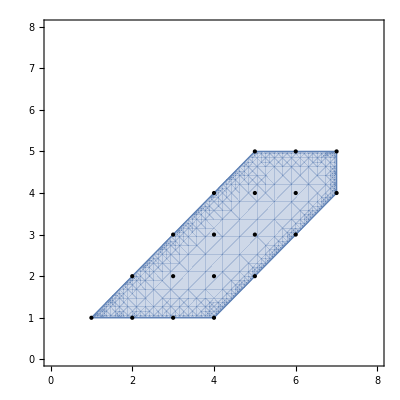

```mathematica
Show[
RegionPlot[iter[i,j],{i,0,8},{j,0,8},MaxRecursion->5],Graphics[Table[If[iter[i,j],Point[{i,j}],{}],{j,0,7},{i,0,7}]]
]
```

```mathematica
g=
Reduce[iter[i,j],{i,j},Integers]
```

(i==1&&j==1)||(i==2&&j==1)||(i==2&&j==2)||(i==3&&j==1)||(i==3&&j==2)||(i==3&&j==3)||(i==4&&j==1)||(i==4&&j==2)||(i==4&&j==3)||(i==4&&j==4)||(i==5&&j==2)||(i==5&&j==3)||(i==5&&j==4)||(i==5&&j==5)||(i==6&&j==3)||(i==6&&j==4)||(i==6&&j==5)||(i==7&&j==4)||(i==7&&j==5)

```mathematica
pieces={i,j}//.{ToRules[g]}
```

{{1,1},{2,1},{2,2},{3,1},{3,2},{3,3},{4,1},{4,2},{4,3},{4,4},{5,2},{5,3},{5,4},{5,5},{6,3},{6,4},{6,5},{7,4},{7,5}}

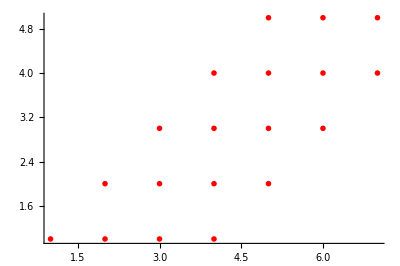

```mathematica
Graphics[{PointSize[0.01],Red,Point[pieces]},Axes->True,AxesOrigin->{0,0}]
```

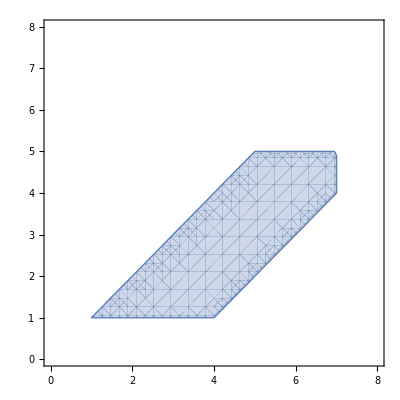

```mathematica
With[{f=Reduce[iter[i,j],{i,j}]},
RegionPlot[f,{i,0,8},{j,0,8}]
]
```

## Visualizing Iteration Space Dependence Graph

Given a program

1. for (int ii = 0; ii < 8; ii++) {
2.   for (int jj = 0; jj < 8; jj++) {
2. 	    a[ii + 1][jj] = a[ii][jj];
3.   }
4. }

We notice that the above is a strong SIV, so we can compute the distance vector

```mathematica
{slopeI,dirI}=StrongSIV[7,Inactivate[1+1*ii],Inactivate[0+1*ii]];
{slopeJ,dirJ}=StrongSIV[7,Inactivate[0+1*jj],Inactivate[0+1*jj]];
```

```mathematica
slope={slopeI,slopeJ}
```

{1,0}

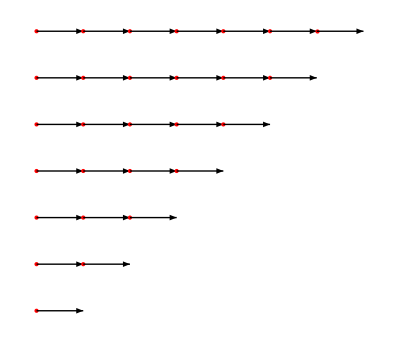

```mathematica
Table[
Table[
{{Red,Point[{ii,jj}]},Arrow[{{ii,jj},{ii,jj}+slope}]},
{jj,ii,7}
],
{ii,7}
]//Graphics
```

If you have a more complicated statement like:

1. for (int ii = 0; ii < 8; ii++) {
2.   for (int jj = 0; jj < 8; jj++) {
2. 	    a[ii + 1][jj] = a[ii + 1][jj] + a[ii][jj+1] + a[ii+1][jj+1];
3.   }
4. }

We just need to compute the LHS relation to all the RHS:

```mathematica
{slopeI1,dirI1}=StrongSIV[7,Inactivate[1+1*ii],Inactivate[0+1*ii]];
{slopeJ1,dirJ1}=StrongSIV[7,Inactivate[0+1*jj],Inactivate[0+1*jj]];
{slopeI2,dirI2}=StrongSIV[7,Inactivate[0+1*ii],Inactivate[0+1*ii]];
{slopeJ2,dirJ2}=StrongSIV[7,Inactivate[0+1*jj],Inactivate[1+1*jj]];
{slopeI3,dirI3}=StrongSIV[7,Inactivate[0+1*ii],Inactivate[1+1*ii]];
{slopeJ3,dirJ3}=StrongSIV[7,Inactivate[0+1*jj],Inactivate[1+1*jj]];
```

```mathematica
slopes={{slopeI1,slopeJ1},{slopeI2,slopeJ2},{slopeI3,slopeJ3}}
```

{{1,0},{0,-1},{-1,-1}}

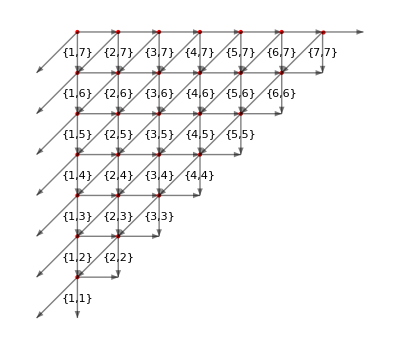

```mathematica
Table[
Table[
{{PointSize[Large],Red,Point[{ii,jj}],Black,Text[{ii,jj},{ii,jj-0.5}]},Opacity[0.5],Arrow[{{ii,jj},{ii,jj}+#}]&/@slopes},
{jj,ii,7}
],
{ii,7}
]//Graphics
```

## Analysis

```mathematica
ClearAll[extractLoopConditions]
extractLoopConditions[___]:={}
extractLoopConditions[
Inactive[For][Inactive[Set][var_,start_],end_,incr_,body_]]:=Module[{iter,this,rest},
iter=var;
this={Inactive[Set][iter,start],end/.{var->iter}};
rest=extractLoopConditions[body]/.{var->iter};
If[rest==={},
{iter,this},
{{iter,Sequence@@First[rest]},Join[this,Last[rest]]}
]
]
```

```mathematica
ClearAll[extractLoopBounds]
extractLoopBounds[x_]:=extractLoopConditions[x]/.{Set->GreaterEqual}
```

```mathematica
i=.;j=.;
loop=Inactivate[
For[i=0,i<7,i++,
For[j=0,j<7,j++,
code
]
]
]
```

For[i=0,i<7,Increment[i],For[j=0,j<7,Increment[j],code]]

```mathematica
extractLoopConditions[loop]
```

{{i,j},{i=0,i<7,j=0,j<7}}

```mathematica
i=.;j=.;
loop=Inactivate[
For[i=0,i<=7,i++,
For[j=Max[i-3,1],j<=Min[i,5],j++,
code
]
]
]
```

For[i=0,i≤7,Increment[i],For[j=Max[i+-3,1],j≤Min[i,5],Increment[j],code]]

```mathematica
PlotIterationSpace2D[x_]:=Module[{r,iter,region,c,p,minX,minY,maxX,maxY},r=extractLoopBounds[loop];
iter=Activate[First[r]];
region=Activate[And@@Last[r]];
c=Reduce[region,iter,Integers];
p=First[r]//.{ToRules[c]};
{{minX,maxX},{minY,maxY}}=Map[Through[{Min,Max}[#]]&,Transpose[p]];
Show[
With[{xhat=First[iter],yhat=Last[iter]},RegionPlot[Evaluate@region,{xhat,minX,maxX},{yhat,minY,maxY},MaxRecursion->5,PlotRange->All]
],
Graphics[{PointSize[Medium],Red,Point[p]}],
PlotRange->All,
AxesOrigin->{0,0},
Axes->True
]
]
PlotIterationSpace3D[x_]:=Module[{r,iter,region,c,p,minX,minY,minZ,maxX,maxY,maxZ},r=extractLoopBounds[loop];
iter=Activate[First[r]];
region=Activate[And@@Last[r]];
c=Reduce[region,iter,Integers];
p=First[r]//.{ToRules[c]};
{{minX,maxX},{minY,maxY},{minZ,maxZ}}=Map[Through[{Min,Max}[#]]&,Transpose[p]];
Show[
With[{xhat=iter[[1]],yhat=iter[[2]],zhat=iter[[3]]},RegionPlot3D[Evaluate@region,{xhat,minX,maxX},{yhat,minY,maxY},{zhat,minZ,maxZ},MaxRecursion->7,PlotPoints->35,PlotStyle->Directive[Yellow,Opacity[0.5]],Mesh->None,PlotRange->All]],
Graphics3D[{PointSize[Medium],Red,Point[p]}],
PlotRange->All,
AxesOrigin->{0,0},
Axes->True
]
]
```

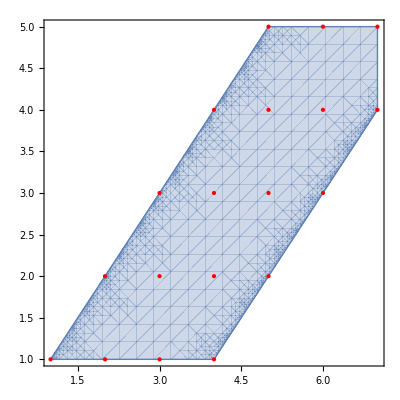

```mathematica
PlotIterationSpace2D[loop]
```

```mathematica
i=.;j=.;z=.;
loop=Inactivate[
For[i=0,i<7,i++,
For[j=Max[i-3,1],j<=Min[i,5],j++,
For[z=Max[i-3,1],z<=Min[j,5],z++,
code
]
]
]
];
extractLoopConditions[loop]
```

{{i,j,z},{i=0,i<7,j=Max[i+-3,1],j≤Min[i,5],z=Max[i+-3,1],z≤Min[j,5]}}

```mathematica
PlotIterationSpace3D[loop]
```

-Graphics3D-

```mathematica
i=.;j=.;z=.;
loop=Inactivate[
For[i=0,i<7,i++,
For[j=i,j≤10,j++,
For[z=Max[i,j],z≤10,z++,
code
]
]
]
];
extractLoopConditions[loop]
```

{{i,j,z},{i=0,i<7,j=i,j≤10,z=Max[i,j],z≤10}}

```mathematica
PlotIterationSpace3D[loop]
```

-Graphics3D-

## Normalize Loop

Procedure in Allen & Kennedy Pg 139

```mathematica
NormalizeLoop[iter_,l_,u_,s_,stmts_]:=
Module[{newL,newU,newStmts},
newL = 0;
newU =FullSimplify[ (u-l+s)/s-1];
newStmts=stmts/.{iter->FullSimplify[iter*s-s+l+1,Assumptions->iter∈Integers]};
Inactivate[For[iter=newL,iter<newU,iter++,
newStmts
]
]
]
NormalizeLoop[Inactive[For][Inactive[Set][iter_,l_],Inactive[Less][iter_,u_],Inactive[AddTo][iter_,s_],stmts_]]:=
NormalizeLoop[iter,l,u,s,stmts]
```

```mathematica
ClearAll[ii]
loop=NormalizeLoop[Inactivate[For[ii=5,ii<10,ii+=1,Print[ii]]]]
```

For[ii=0,ii<5,Increment[ii],Print[5+ii]]

```mathematica
Activate[loop]
```

5

6

7

8

9

```mathematica
ClearAll[ii]
For[ii=5,ii<10,ii+=1,Print[ii]]
```

5

6

7

8

9

## End Of Chapter Questions

### 5.1

```mathematica
ClearAll[s1,s2,s4,s6,s8,a,b,c,d,e]
```

```mathematica
s1=Inactivate[b=a*2];
s2=Inactivate[c=b+1];
s4=Inactivate[b=c+1];
s6=Inactivate[b=b-1];
s8=Inactivate[e=b-d];
```

The dependence graph is (note that this is the answer, but there is not flow dependence (or anti-dependence) between s4 and s6, since they are mutually exclusive).

```mathematica
DependenceGraph[{s1,s2,s4,s6,s8}]
```

-Graphics-

### 5.2

First, normalize the loop, define a function j(i) = i - 3 so j^-1(i) = i + 3 . Now, substitute all i with j^-1(i). The loop is now transformed to

1. for (int j = 0; j < N - 3; j++) {
2. 	 a[j + 3] = (a[j + 1] + a[j + 5])/2;
3. }

```mathematica
ClearAll[j]
With[{n=10},
{
StrongSIV[n,Inactivate[3+1*j],Inactivate[1+1*j]],
StrongSIV[n,Inactivate[3+1*i],Inactivate[5+1*i]]
}
]
```

{{2,<},{-2,<}}

So, is the direction vector {2} or {-2} ????? How do you determine the direction vector if you do not know the upper bound??

### 5.3

```mathematica
distances={2,-2};
```

```mathematica
With[{n=10},
Graphics[{
Line[{{0,0},{n,0}}],
Table[{
{Opacity[0.5],Arrowheads[Small],Arrow[BezierCurve[{{j,0},{j+#/2,#/2},{j+#,0}}]]&/@distances},
{PointSize[Large],Red,Point[{j,0}],Black,Text[Style[j,Bold],{j,-0.5}]}
},
{j,0,n}
]
}]
]
```

-Graphics-

### 5.4

First, normalize the loop

```mathematica
ClearAll[ii,n,a]
NormalizeLoop[Inactivate[
For[ii=3,ii<n,ii+=2,
a[[ii]]=(a[[ii-1]]+a[[ii+1]])/2
]
]]
```

For[ii=0,ii<1/2 (-3+n),Increment[ii],Inactivea2 (1+ii)=(Inactivea2 (1+ii)+-1+Inactivea2 (1+ii)+1)*2^(-1)]

It is annoying that the normalization does not place things in SIV form, but we get

```mathematica
ClearAll[ii]
{
StrongSIV[10,Inactivate[2+2*ii],Inactivate[1+2*ii]],
StrongSIV[10,Inactivate[2+2*ii],Inactivate[3+2*ii]]
}
```

{{1/2,Unknown},{-1/2,Unknown}}

There is no dependence

### 5.6

First, normalize the loop

```mathematica
ClearAll[ii,n,a]
NormalizeLoop[Inactivate[
For[ii=3,ii<n,ii+=2,
a[[ii]]=(a[[ii-2]]+a[[ii+2]])/2
]
]]
```

For[ii=0,ii<1/2 (-3+n),Increment[ii],Inactivea2 (1+ii)=(Inactivea2 (1+ii)+-2+Inactivea2 (1+ii)+2)*2^(-1)]

It is annoying that the normalization does not place things in SIV form, but we get

```mathematica
ClearAll[ii]
With[{n=10},
{
StrongSIV[10,Inactivate[2+2*ii],Inactivate[0+2*ii]],
StrongSIV[10,Inactivate[2+2*ii],Inactivate[4+2*ii]]
}
]
```

{{1,<},{-1,<}}

### 5.7

```mathematica
distances={1,-1};
```

```mathematica
With[{n=10},
Graphics[{
Line[{{0,0},{n,0}}],
Table[{
{Opacity[0.5],Arrowheads[Small],Arrow[BezierCurve[{{j,0},{j+#/2,#/2},{j+#,0}}]]&/@distances},
{PointSize[Large],Red,Point[{j,0}],Black,Text[Style[j,Bold],{j,-0.5}]}
},
{j,0,n}
]
}]
]
```

-Graphics-